```mathematica
allGraphs5[0,"children"]
```

{{19683,39366},{6561,13122},{2187,4374},{729,1458},{243,486},{81,162},{27,54},{9,18},{3,6},{1,2}}

```mathematica
allGraphs5[0,"matrix"]
```

{{2,0,0,0,0},{0,2,0,0,0},{0,0,2,0,0},{0,0,0,2,0},{0,0,0,0,2}}

```mathematica
allGraphs5[19683,"matrix"]//MatrixForm
```

(2 | 1 | 0 | 0 | 0
1 | 2 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0
0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 2)

```mathematica
allGraphs5[39366,"matrix"]
```

{{2,2,0,0,0},{2,2,0,0,0},{0,0,2,0,0},{0,0,0,2,0},{0,0,0,0,2}}

```mathematica
allGraphs5[19683,"matrix"]+{{2,-1,0,0,0},{-1,2,0,0,0},{0,0,2,0,0},{0,0,0,2,0},{0,0,0,0,2}}//MatrixForm
```

(4 | 0 | 0 | 0 | 0
0 | 4 | 0 | 0 | 0
0 | 0 | 4 | 0 | 0
0 | 0 | 0 | 4 | 0
0 | 0 | 0 | 0 | 4)

```mathematica
MatrixForm[allGraphs5[alfaKey,"matrix"]]
```

(2 | 1 | 2 | 1 | 1
1 | 2 | 1 | 0 | 0
2 | 1 | 2 | 1 | 1
1 | 0 | 1 | 2 | 1
1 | 0 | 1 | 1 | 2)

```mathematica
allGraphs5[alfaKey,"children"]
```

{{36058,36166},{36004,36112}}

```mathematica
Solve[allGraphs5[36058,"matrix"].x==allGraphs5[36166,"matrix"],x]
```

{}

```mathematica
allGraphs5[36166,"colofour"]
```

v13x24x5

```mathematica
h=(allGraphs5[36058,"colofour"]//ZetaFunctionFromFormula);
```

```mathematica
h2=(allGraphs5[36166,"colofour"]//ListofVars//ZetaFunctionFromFormula);
```

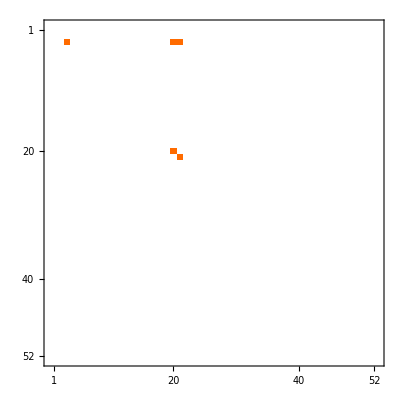

```mathematica
(allGraphs5[alfaKey,"colofour"]//ListofVars//ZetaFunctionFromFormula)//MatrixPlot
```

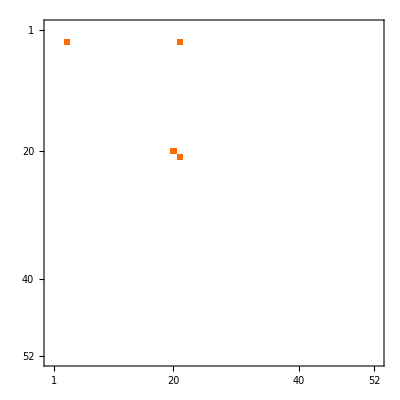

```mathematica
h+h2//MatrixPlot
```

```mathematica
allGraphs5[alfaKey,"graph"]
```

-Graphics-

```mathematica
(PseudoInverse[allGraphs5[alfaKey,"matrix"]].allGraphs5[36058,"matrix"]).allGraphs5[36166,"matrix"]//MatrixForm
```

(3/2 | 0 | 3/2 | 0 | 1/2
2 | 4 | 2 | 4 | 2
3/2 | 0 | 3/2 | 0 | 1/2
2 | 4 | 2 | 4 | 2
1 | 1 | 1 | 1 | 2)

```mathematica
PseudoInverse[allGraphs5[36058,"matrix"]].allGraphs5[36166,"matrix"]//MatrixForm
```

(1/2 | -1/4 | 1/2 | -1/4 | -1/4
0 | 1 | 0 | 1 | 1
1/2 | -1/4 | 1/2 | -1/4 | -1/4
0 | 1/2 | 0 | 1/2 | -1/2
0 | 1/2 | 0 | 1/2 | 3/2)

```mathematica
PseudoInverse[allGraphs5[36166,"matrix"]].allGraphs5[36058,"matrix"]//MatrixForm
```

(1/2 | 3/16 | 1/2 | 1/16 | 1/16
0 | 7/16 | 0 | 5/16 | -3/16
1/2 | 3/16 | 1/2 | 1/16 | 1/16
0 | 7/16 | 0 | 5/16 | -3/16
0 | -5/8 | 0 | 1/8 | 9/8)

```mathematica
Map[MatrixForm[IntegerPart[(MakeOffDiagnoal2Negative[allGraphs5[#[[1]],"matrix"]]+MakeOffDiagnoal2Negative[allGraphs5[#[[2]],"matrix"]])/2]]&,allGraphs5[alfaKey,"children"]]
```

{(2 | 1 | -1 | 1 | 1
1 | 2 | 1 | 0 | 0
-1 | 1 | 2 | 1 | 1
1 | 0 | 1 | 2 | 1
1 | 0 | 1 | 1 | 2),(2 | 1 | -1 | 1 | 1
1 | 2 | 1 | 0 | 0
-1 | 1 | 2 | 1 | 1
1 | 0 | 1 | 2 | 1
1 | 0 | 1 | 1 | 2)}

```mathematica
Map[MatrixForm[IntegerPart[(MakeOffDiagnoal2Negative[allGraphs5[#[[1]],"matrix"]]+MakeOffDiagnoal2Negative[allGraphs5[#[[2]],"matrix"]])/2]]&,allGraphs5[betaKey,"children"]]
```

{(2 | 1 | 1 | -1 | 1
1 | 2 | 1 | 1 | 0
1 | 1 | 2 | 1 | 0
-1 | 1 | 1 | 2 | 1
1 | 0 | 0 | 1 | 2),(2 | 1 | 1 | -1 | 1
1 | 2 | 1 | 1 | 0
1 | 1 | 2 | 1 | 0
-1 | 1 | 1 | 2 | 1
1 | 0 | 0 | 1 | 2)}

```mathematica
MatrixForm[IntegerPart[(MakeOffDiagnoal2Negative[allGraphs5[19683,"matrix"]]+MakeOffDiagnoal2Negative[allGraphs5[39366,"matrix"]])/2]]
```

(2 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0
0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 2)

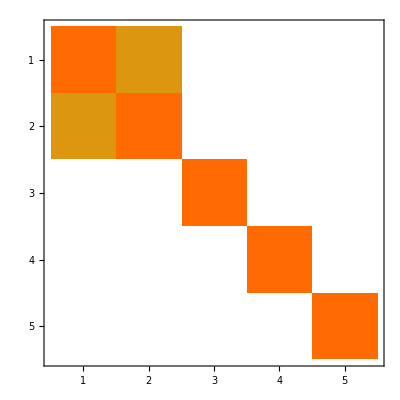

```mathematica
allGraphs5[19683,"matrix"]+allGraphs5[39366,"matrix"]//MatrixPlot
```

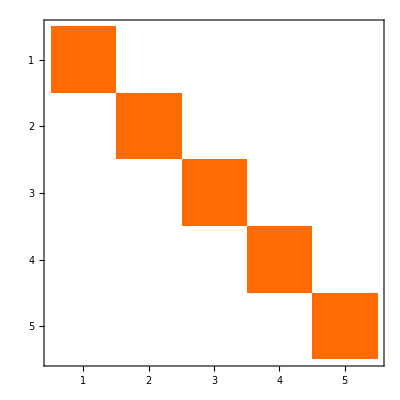

```mathematica
allGraphs5[0,"matrix"]//MatrixPlot
```

```mathematica
allGraphs5[0,"colofour"]
```

v12345+v1234x5+v1235x4+v123x45+v123x4x5+v1245x3+v124x35+v124x3x5+v125x34+v125x3x4+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v1345x2+v134x25+v134x2x5+v135x24+v135x2x4+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v145x23+v145x2x3+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x2345+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5

```mathematica
allGraphs5[19683,"colofour"]+allGraphs5[39366,"colofour"]
```

v12345+v1234x5+v1235x4+v123x45+v123x4x5+v1245x3+v124x35+v124x3x5+v125x34+v125x3x4+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v1345x2+v134x25+v134x2x5+v135x24+v135x2x4+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v145x23+v145x2x3+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x2345+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5

```mathematica
MakeOffDiagnoal2Negative[mat_]:=Table[
If[i==j,mat[[i,j]],
If[mat[[i,j]]==2,-1,mat[[i,j]]]
],
{i,Length[mat]},{j,Length[mat]}
]
```

```mathematica
MakeOffDiagnoal2Negative[allGraphs5[39366,"matrix"]]//MatrixForm
```

(2 | -1 | 0 | 0 | 0
-1 | 2 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0
0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 2)

```mathematica
allGraphs5[lambdaKey,"children"]
```

{{27226,35977},{22852,31681},{20746,23041},{20692,20803},{20668,27259}}

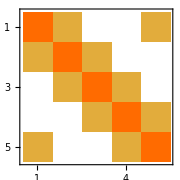

```mathematica
MakeOffDiagnoal2Negative[allGraphs5[lambdaKey,"matrix"]]//MatrixPlot
```

```mathematica
Doit[k_]:={ShowGraph5Least[k],MatrixForm[allGraphs5[k,"matrix"]],MatrixPlot[allGraphs5[k,"matrix"]],MatrixForm[MakeOffDiagnoal2Negative[allGraphs5[k,"matrix"]]]}
```

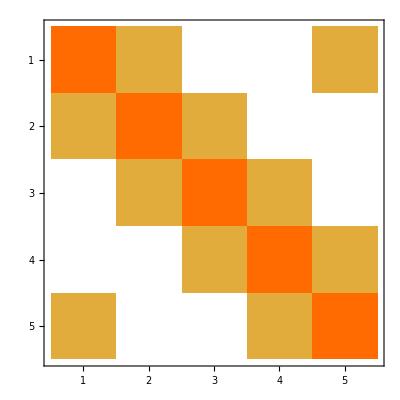
{-Graphics-206653,(2 | 1 | 0 | 0 | 1
1 | 2 | 1 | 0 | 0
0 | 1 | 2 | 1 | 0
0 | 0 | 1 | 2 | 1
1 | 0 | 0 | 1 | 2),-Graphics-,(2 | 1 | 0 | 0 | 1
1 | 2 | 1 | 0 | 0
0 | 1 | 2 | 1 | 0
0 | 0 | 1 | 2 | 1
1 | 0 | 0 | 1 | 2)}

```mathematica
Doit[lambdaKey]
```

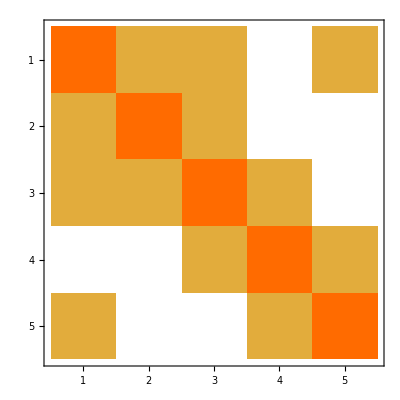
{-Graphics-272262,(2 | 1 | 1 | 0 | 1
1 | 2 | 1 | 0 | 0
1 | 1 | 2 | 1 | 0
0 | 0 | 1 | 2 | 1
1 | 0 | 0 | 1 | 2),-Graphics-,(2 | 1 | 1 | 0 | 1
1 | 2 | 1 | 0 | 0
1 | 1 | 2 | 1 | 0
0 | 0 | 1 | 2 | 1
1 | 0 | 0 | 1 | 2)}

```mathematica
Doit[27226]
```

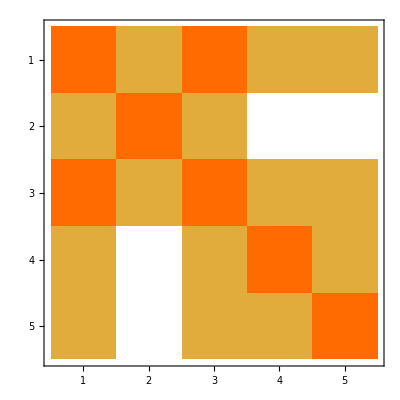
{-Graphics-359771,(2 | 1 | 2 | 1 | 1
1 | 2 | 1 | 0 | 0
2 | 1 | 2 | 1 | 1
1 | 0 | 1 | 2 | 1
1 | 0 | 1 | 1 | 2),-Graphics-,(2 | 1 | -1 | 1 | 1
1 | 2 | 1 | 0 | 0
-1 | 1 | 2 | 1 | 1
1 | 0 | 1 | 2 | 1
1 | 0 | 1 | 1 | 2)}

```mathematica
Doit[35977]
```

```mathematica
MatrixForm[IntegerPart[(MakeOffDiagnoal2Negative[allGraphs5[27226,"matrix"]]+MakeOffDiagnoal2Negative[allGraphs5[35977,"matrix"]])/2]]
```

(2 | 1 | 0 | 0 | 1
1 | 2 | 1 | 0 | 0
0 | 1 | 2 | 1 | 0
0 | 0 | 1 | 2 | 1
1 | 0 | 0 | 1 | 2)

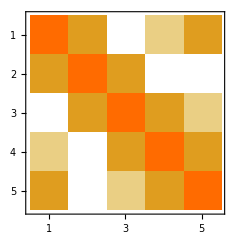

```mathematica
MakeOffDiagnoal2Negative[allGraphs5[27226,"matrix"]]+MakeOffDiagnoal2Negative[allGraphs5[35977,"matrix"]]//MatrixPlot
```

```mathematica
MakeOffDiagnoal2Negative[allGraphs5[lambdaKey,"matrix"]]
```

{{2,1,0,0,1},{1,2,1,0,0},{0,1,2,1,0},{0,0,1,2,1},{1,0,0,1,2}}

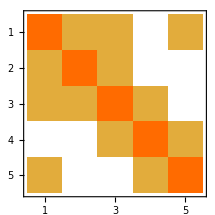

```mathematica
MakeOffDiagnoal2Negative[allGraphs5[27226,"matrix"]]//MatrixPlot
```

```mathematica
allGraphs5[35977,"matrix"]//MatrixForm
```

(2 | 1 | 2 | 1 | 1
1 | 2 | 1 | 0 | 0
2 | 1 | 2 | 1 | 1
1 | 0 | 1 | 2 | 1
1 | 0 | 1 | 1 | 2)

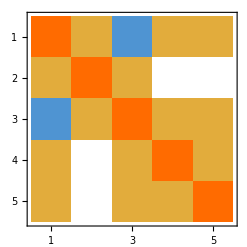

```mathematica
MakeOffDiagnoal2Negative[allGraphs5[35977,"matrix"]]//MatrixPlot
```

```mathematica
ShowGraph5Least[27226]
```

-Graphics-272262

```mathematica
allGraphs5[27226,"colofour"]/.RepGraph["C"]
```

-Graphics-317380+-Graphics-317140+-Graphics-296080+-Graphics-317110+-Graphics-296050+-Graphics-295510+-Graphics-295270+-Graphics-295240

```mathematica
allGraphs5[amigo1,"colofour"]/.RepGraph["C"]
```

-Graphics-296080+-Graphics-296050+-Graphics-295510+-Graphics-295270+-Graphics-295240